## notes

mire vagyunk kíváncsiak?
- hogyan termel a napelem --> szimulációt kell összehasonlítani a teljesítménnyel
	- szimuláció: adott
	- teljesítmény: napi adat adott, jó lenne stringenként és 5 perces bontásban
- mennyit tudunk megtakarítani, milyen lesz kb a cash-flow
	- Kazános vs. Gólyás fogyasztás szétválasztva
		- visszamenőlegesen összes rezsiadat kellene, ez alapján becsülni
	- MVM-től havi átalány
		- szerződésből látszik / Flórától kérdezni
	- leadott és felvett áram szaldós elszámolása évente egyszer október elején (?)
		- E.On-tól letölthetőek eddigiek
		- ezutániak termelési becslésből és almérők adataiból becsülhetők

adott időintervallumra:
	production + takeup = consumption + feedin
	
	consumption = production + takeup - feedin
	
	consumption = Kazán_consumption + Gólya_consumption
	
	Kazán_consumption = Σ Kazán_almérő_i
	
	Gólya_consumption = consumption - Kazán_consumption = consumption - Σ Kazán_almérő_i = production + takeup - feedin - Σ Kazán_almérő_i

## functions

```mathematica
Difference[tuple_]:=If[Length[tuple]==2,tuple[[1]]-tuple[[2]],tuple[[1]]]
Ratio[tuple_]:=If[Length[tuple]==2&&tuple[[2]]!=0,tuple⟦1⟧/tuple⟦2⟧,Nothing]
```

```mathematica
MergeDateValueLists[operation_,granularity_:"Day",lists_]:=
Module[
{combinedLists,groupedByDate,normalizedDates},
(*Flatten the lists and normalize DateObjects to the specified granularity*)
combinedLists=Flatten[lists,1];
normalizedDates=({DateObject[#,granularity],#2}&@@@combinedLists);
(*Group by normalized DateObject*)
groupedByDate=GatherBy[normalizedDates,First];
(*Merge values that have the same DateObject using the specified operation*)
Select[Map[KeyValueMap[List,#][[1]]&,Merge[Rule@@@#,operation]&/@groupedByDate],Length[#]==2&]
]
```

```mathematica
StripDateToGranularity[data_List,granularity_String]:=Module[
{adjustedDates},
(*Adjust each DateObject to the specified granularity*)
adjustedDates=({DateObject[#,granularity],#2}&@@@data);
adjustedDates
]
```

```mathematica
MapFunctionToGranularity[function_,data_List,granularity_String]:=Module[
{extractedComponents,groupedData,mappedData},
(*Extract the relevant component (e.g.,month) from each DateObject and pair with value*)extractedComponents=({DateValue[#[[1]],granularity],#[[2]]}&/@data);
(*Group data by the extracted component and calculate the mean for each group*)
groupedData=GroupBy[extractedComponents,First->Last];
(*Replace each group key with an average value*)
mappedData=function/@groupedData;
SortBy[Transpose[{Keys[mappedData],Values[mappedData]}],First]
]
```

```mathematica
DateBetween[testDate_,{startDate_,endDate_}]:=startDate<=testDate<=endDate
```

```mathematica
TimestampedDataToUnixTime[data_]:=Transpose[{
Map[UnixTime,Transpose[data][[1]]],
Transpose[data][[2]]
}]
```

```mathematica
UnixTimeDataToTimestamped[data_]:=Transpose[{
Map[FromUnixTime,Transpose[data][[1]]],
Transpose[data][[2]]
}]
```

## load data & set variables

### etc

```mathematica
years={2019,2020,2021,2022,2023,2024};
```

```mathematica
months=Range[12];
```

```mathematica
monthLengths={31,28,31,30,31,30,31,31,30,31,30,31};
```

```mathematica
monthNames={"Jan","Feb","Márc","Ápr","Máj","Jún","Júl","Aug","Szept","Okt","Nov","Dec"};
```

```mathematica
timezoneShiftHour=DateObject[{2024,3,31,2,0,0}];
```

```mathematica
entsoeDataHeader=Import[NotebookDirectory[]<>"input\\monthly_hourly_load_values_2023.csv"][[1]];
entsoeLoadData=Select[Import[NotebookDirectory[]<>"input\\monthly_hourly_load_values_2023.csv"],#[[6]]=="HU"&];
```

```mathematica
entsoeLoadHourly2023=Transpose[{
Transpose[StripDateToGranularity[Quiet[Map[DateObject,Transpose[entsoeLoadData][[2]]]],"Hour"]][[1]],
Transpose[entsoeLoadData][[8]]
}];
```

### PV

#### simulation

```mathematica
simulatedCapacity=33.6;
```

```mathematica
simulatedPerformance=Import[NotebookDirectory[]<>"input\\PV\\simulation.csv"];
```

```mathematica
installedCapacity=36.08;
```

```mathematica
capacityCorrection=installedCapacity/simulatedCapacity;
```

```mathematica
simulatedMidmonthProduction=Table[
{
DateDifference[DateObject[{2024,1,1}],DateObject[{2024,month,monthLengths[[month]]/2}]][[1]]+1,
(1000Transpose[simulatedPerformance][[-2]][[2+1;;2+12]]capacityCorrection)[[month]]/monthLengths[[month]]
}
,{month,1,12}];
SimulatedDailyProduction[day_Integer]:=Quiet[Interpolation[simulatedMidmonthProduction,InterpolationOrder->1][day]];
SimulatedDailyProduction[date_DateObject]:=Module[{dayOfYear},(*Convert DateObject to day of year*)dayOfYear=DateValue[date,"DayOfYear"];
(*Call the original function using the computed day of year*)SimulatedDailyProduction[dayOfYear]];
```

#### production

```mathematica
productionStart=DateObject[{2024,1,2}];
```

```mathematica
stringFixDay=DateObject[{2024,4,3}];
```

```mathematica
extractionFiles=FileNames[All,NotebookDirectory[]<>"input\\pv\\his_inv\\extracted\\"];
```

```mathematica
extractionImports=Map[
Reverse[Flatten[Import[#]]]
&,
extractionFiles
];
```

```mathematica
extractionImport=extractionImports[[2]];
```

```mathematica
lines=Map[Reverse,ArrayReshape[
extractionImport,
{4320,30}
]];
```

```mathematica
lines2=Map[
Flatten[{
FromUnixTime[#[[1]]],
#[[2;;-1]]
}]&
,lines];
```

```mathematica
lines3=Select[lines2,DateBetween[#[[1]],{DateObject[{2024,3,17,0,0,0}],DateObject[{2024,3,17,23,59,59}]}]&];
```

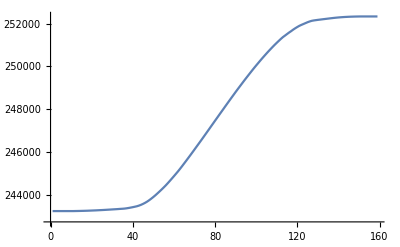

```mathematica
ListPlot[Transpose[lines3][[2]],Joined->True]
```

```mathematica
gridFreq5Minutes=SortBy[DeleteDuplicates[Flatten[Table[
Module[
{lines},
lines=Map[Reverse,ArrayReshape[
extractionImport,
{4320,30}
]];
Transpose[{
Map[
If[
FromUnixTime[#]<=timezoneShiftHour,
DatePlus[FromUnixTime[#],{-1,"Hour"}],
DatePlus[FromUnixTime[#],{-2,"Hour"}]
]
&,Transpose[lines][[1]]],
Transpose[lines][[18]]/6553600
}]
],{extractionImport,extractionImports}],1]],First];
```

```mathematica
gridFreqHourly=StripDateToGranularity[TimeSeriesAggregate[gridFreq5Minutes,"Hour",Mean],"Hour"];
```

```mathematica
production5Minutes=SortBy[DeleteDuplicates[Flatten[Table[
Module[
{lines},
lines=Map[Reverse,ArrayReshape[
extractionImport,
{4320,30}
]];
Transpose[{
Drop[Map[
If[
FromUnixTime[#]<=timezoneShiftHour,
DatePlus[FromUnixTime[#],{-1,"Hour"}],
DatePlus[FromUnixTime[#],{-2,"Hour"}]
]
&,Transpose[lines][[1]]],1],
Differences[Transpose[lines][[2]]]/100
}]
],{extractionImport,extractionImports}],1]],First];
```

```mathematica
manualProductionData=Quiet[Map[
{
If[
StripDateToGranularity[{DateObject[#[[1]]]},"Hour"][[1]][[1]]<=timezoneShiftHour,
DatePlus[StripDateToGranularity[{DateObject[#[[1]]]},"Hour"][[1]][[1]],{-1,"Hour"}],
DatePlus[StripDateToGranularity[{DateObject[#[[1]]]},"Hour"][[1]][[1]],{-2,"Hour"}]
],
#[[2]]
}&,
DeleteCases[Import[NotebookDirectory[]<>"input\\pv\\manual\\manual_extraction.csv"],{"",""}]
]];
```

```mathematica
productionHourly=Map[
{
#[[1]][[1]],
Total[Transpose[#][[2]]]
}
&,GatherBy[SortBy[Join[manualProductionData,StripDateToGranularity[TimeSeriesAggregate[production5Minutes,"Hour",Total],"Hour"]],First],First]
];
```

```mathematica
productionDaily=SortBy[TimeSeriesAggregate[productionHourly,"Day",Total],First];
```

```mathematica
productionWeekly=SortBy[TimeSeriesAggregate[productionHourly,"Week",Total],First];
```

```mathematica
productionMonthly=SortBy[TimeSeriesAggregate[productionHourly,"Month",Total],First];
```

### grid

```mathematica
ganzData=Drop[Import[NotebookDirectory[]<>"input\\grid\\takeup_ganz.csv"],1];
```

```mathematica
ganzTakeupMonthly=Drop[Map[{DateObject[{#[[1]],#[[2]]}],#[[3]]}&,ganzData],1];
```

```mathematica
eonData=Map[StringSplit[#,";"][[1]]&,Import[NotebookDirectory[]<>"input\\grid\\eon_export.csv"]];
```

```mathematica
takeup15MinutesUnixTimeBlocky=Map[{UnixTime[DateObject[#[[3]]]],ToExpression[#[[4]]]}&,Select[eonData,#[[2]]=="'+A'"&]];
takeup15MinutesUnnormalized=UnixTimeDataToTimestamped[MovingAverage[takeup15MinutesUnixTimeBlocky,20]];
(*takeup15MinutesUnnormalized=UnixTimeDataToTimestamped[takeup15MinutesUnixTimeBlocky];*)
takeup15Minutes=Transpose[{
Transpose[takeup15MinutesUnnormalized][[1]],
Transpose[takeup15MinutesUnnormalized][[2]](Total[Transpose[takeup15MinutesUnixTimeBlocky][[2]]]/Total[Transpose[takeup15MinutesUnnormalized][[2]]])
}];
```

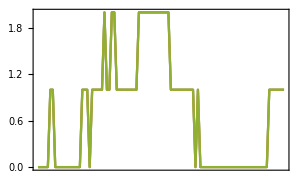

```mathematica
DateListPlot[
{
UnixTimeDataToTimestamped[takeup15MinutesUnixTimeBlocky[[1100;;1200]]],
takeup15MinutesUnnormalized[[1100;;1200]],
takeup15Minutes[[1100;;1200]]
}
]
```

```mathematica
takeupHourly=StripDateToGranularity[TimeSeriesAggregate[takeup15Minutes,"Hour",Total],"Hour"];
```

```mathematica
takeupDaily=StripDateToGranularity[TimeSeriesAggregate[takeup15Minutes,"Day",Total],"Day"];
```

```mathematica
takeupWeekly=StripDateToGranularity[TimeSeriesAggregate[takeup15Minutes,"Week",Total],"Week"];
```

```mathematica
takeupMonthly=StripDateToGranularity[MergeDateValueLists[
Total,
"Month",
{
ganzTakeupMonthly,
TimeSeriesAggregate[takeup15Minutes,"Month",Total]
}
],"Month"];
```

```mathematica
feedin15MinutesUnixTimeBlocky=Map[{UnixTime[DateObject[#[[3]]]],ToExpression[#[[4]]]}&,Select[eonData,#[[2]]=="'-A'"&]];
feedin15MinutesUnnormalized=UnixTimeDataToTimestamped[MovingAverage[feedin15MinutesUnixTimeBlocky,20]];
(*feedin15MinutesUnnormalized=UnixTimeDataToTimestamped[feedin15MinutesUnixTimeBlocky];*)
feedin15Minutes=Transpose[{
Transpose[feedin15MinutesUnnormalized][[1]],
Transpose[feedin15MinutesUnnormalized][[2]](Total[Transpose[feedin15MinutesUnixTimeBlocky][[2]]]/Total[Transpose[feedin15MinutesUnnormalized][[2]]])
}];
```

```mathematica
feedinHourly=StripDateToGranularity[TimeSeriesAggregate[feedin15Minutes,"Hour",Total],"Hour"];
```

```mathematica
feedinDaily=StripDateToGranularity[TimeSeriesAggregate[feedin15Minutes,"Day",Total],"Day"];
```

```mathematica
feedinWeekly=StripDateToGranularity[TimeSeriesAggregate[feedin15Minutes,"Week",Total],"Week"];
```

```mathematica
feedinMonthly=StripDateToGranularity[TimeSeriesAggregate[feedin15Minutes,"Month",Total],"Month"];
```

### consumption

```mathematica
submeterReadings=Drop[Import[NotebookDirectory[]<>"input\\consumption\\submeter_readings.csv"],1];
```

```mathematica
submeterDecode=Flatten[Map[{#[[1]]->#[[2]],#[[2]]->#[[1]]}&,Drop[Import[NotebookDirectory[]<>"input\\consumption\\submeter_decode.csv"],1]]];
```

```mathematica
users=Join[Transpose[Drop[Import[NotebookDirectory[]<>"input\\consumption\\submeter_decode.csv"],1]][[2]]];
```

```mathematica
consumptionBySubmeterMonthly=Table[
Map[
{
DateObject[#[[1;;2]]],
#[[3]]
}
&,Transpose[Join[
Transpose[Drop[submeterReadings,1]][[{1,2}]],{Differences[Transpose[Transpose[submeterReadings][[2+(users[[user]]/.Flatten[submeterDecode])]]]]}
]]
]
,{user,1,10}];
```

```mathematica
kazanConsumptionMonthly=StripDateToGranularity[MergeDateValueLists[Total,"Month",consumptionBySubmeterMonthly],"Month"];
```

```mathematica
consumptionHourly=StripDateToGranularity[MergeDateValueLists[
Difference,
"Hour",
{
MergeDateValueLists[Total,"Hour",{takeupHourly,productionHourly}],
feedinHourly
}
],"Hour"];
```

```mathematica
consumptionDaily=StripDateToGranularity[MergeDateValueLists[
Difference,
"Day",
{
MergeDateValueLists[Total,"Day",{takeupDaily,productionDaily}],
feedinDaily
}
],"Day"];
```

```mathematica
consumptionWeekly=StripDateToGranularity[TimeSeriesAggregate[consumptionDaily,"Week",Total],"Week"];
```

```mathematica
consumptionMonthly=StripDateToGranularity[MergeDateValueLists[
Difference,
"Month",
{
MergeDateValueLists[
Total,
"Month",
{
productionMonthly,
takeupMonthly
}
],
feedinMonthly
}
],"Month"];
```

```mathematica
golyaConsumptionMonthly=StripDateToGranularity[MergeDateValueLists[
Difference,
"Month",
{
consumptionMonthly,
kazanConsumptionMonthly
}
],"Month"];
```

## PV performace v. simulation (needs DateObject fix)

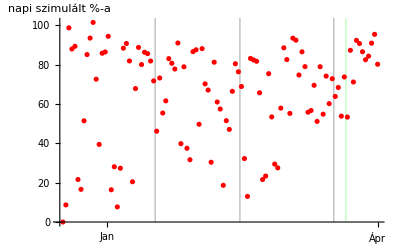

```mathematica
relativePerformance=ListPlot[Map[
#[[2]]/SimulatedDailyProduction[#[[1]]]
&,dailyProduction
],PlotStyle->Red,AxesLabel->{None,"napi szimulált %-a"},ImageSize->400,
Ticks->{
Table[{Accumulate[monthLengths][[month]]-monthLengths[[month]]/2,monthNames[[month]]},{month,1,12}],Transpose[{Range[0,1,0.2],Round[100Range[0,1,0.2]]}]
},
Prolog->{
RGBColor[0,0,0,0.25],
Table[Line[{{month+0.5,0},{month+0.5,200}}],{month,Accumulate[monthLengths]}],
Green,Line[{{stringFixDay+0.5,0},{stringFixDay+0.5,200}}]
}
]
```

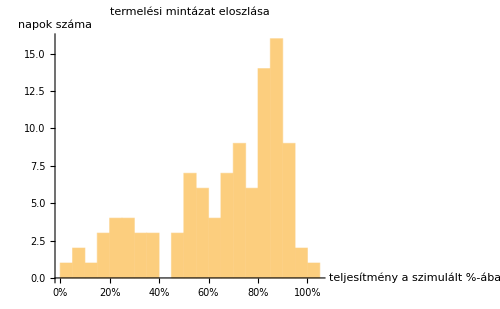

```mathematica
relativePerformanceDistribution=Histogram[
Map[
#[[2]]/SimulatedDailyProduction[#[[1]]]
&,dailyProduction
],25,
AxesLabel->{"teljesítmény a\nszimulált %-ában","napok száma"},
Ticks->{Map[{#,ToString[Round[100#]]<>"%"}&,Range[0,1,0.2]],Automatic},ImageSize->500,
PlotLabel->"termelési mintázat eloszlása"
]
```

```mathematica
dailyProduction[[dailyProduction[[-1]][[1]]]][[2]]/SimulatedDailyProduction[dailyProduction[[-1]][[1]]]
```

0.801974

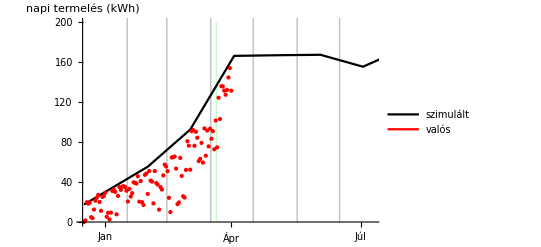

```mathematica
absolutePerformance=ListPlot[
{
Table[SimulatedDailyProduction[day],{day,0,365}],
 dailyProduction,
{{-10,10}}
},PlotRange->{{0,dailyProduction[[-1]][[1]]+100},{0,200}},Joined->{True,False,True},PlotStyle->{{Thick,Black},{PointSize->0.01,Red},Red},ImageSize->400,AxesLabel->{None,"napi termelés\n(kWh)"},
Ticks->{
Table[{Accumulate[monthLengths][[month]]-monthLengths[[month]]/2,monthNames[[month]]},{month,1,12}],
Automatic
},
Prolog->{
RGBColor[0,0,0,0.25],
Table[Line[{{month+0.5,0},{month+0.5,300}}],{month,Accumulate[monthLengths]}],
Green,Line[{{stringFixDay+0.5,0},{stringFixDay+0.5,200}}]
},
PlotLegends->Placed[{"szimulált",None,"valós"},Bottom]
]
```

```mathematica
SimulatedDailyProduction[dailyProduction[[-1]][[1]]]
```

164.095

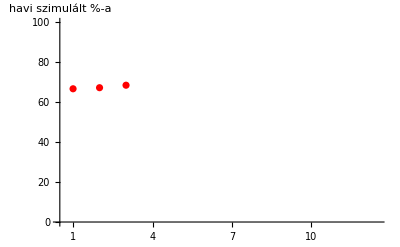

```mathematica
ListPlot[
Table[
N[Total[Transpose[dailyProduction][[2]][[
If[month==1,1,Accumulate[monthLengths][[month-1]]];;
Accumulate[monthLengths][[month]]
]]]]/(1000Transpose[simulatedPerformance][[-2]][[2+1;;2+12]]capacityCorrection)[[month]]
,{month,1,3}],
PlotStyle->Red,AxesLabel->{None,"havi szimulált %-a"},ImageSize->400,
Ticks->{
Range[12],Transpose[{Range[0,1,0.2],Round[100Range[0,1,0.2]]}]
},PlotRange->{{0.5,12.5},{0,1}}
]
```

```mathematica
typicalDailyProductionByMonth=Table[
Transpose[
Drop[
Map[
{#[[1]]+0.5,#[[2]],If[Length[#]==3,#[[3]],0]}&,
SortBy[
Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,Select[
productionHourly,
DateValue[#[[1]],"Month"]==month&
],"Hour"]]
,First]
]
,1]
]
,{month,{1,2,3,4}}];
```

```mathematica
ErrorListPlot[
typicalDailyProductionByMonth,
{Red,Green,Black,Blue,Orange,Purple,Pink},
{PlotLegends->monthNames[[1;;4]],PlotLabel->"megtermelt áram tipikus napi lefutása hónaponként",ImageSize->500},
{True,True,False}
]
```

-Graphics-

## takeup, production, consumption, feedin

### historical

takeup + production = consumption + feedin

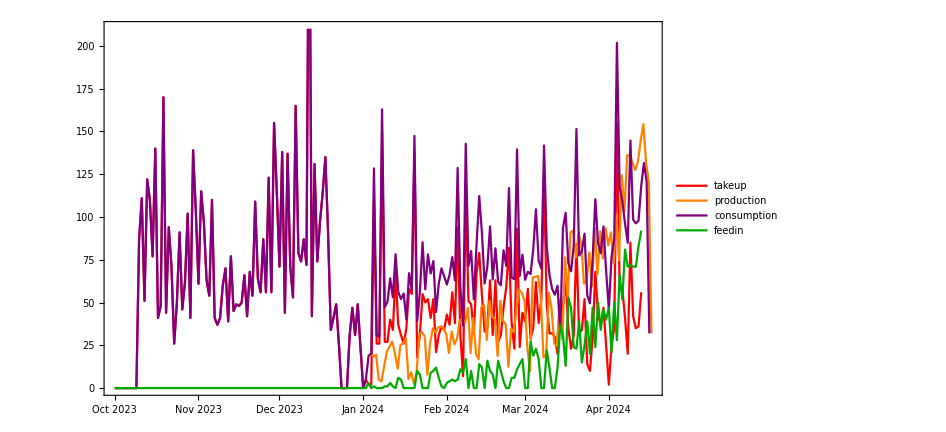

```mathematica
DateListPlot[
{takeupDaily,productionDaily,consumptionDaily,feedinDaily},
PlotStyle->{Red,Orange,Purple,Darker[Green]},
PlotLegends->{"takeup","production","consumption","feedin"},
ImageSize->700
]
```

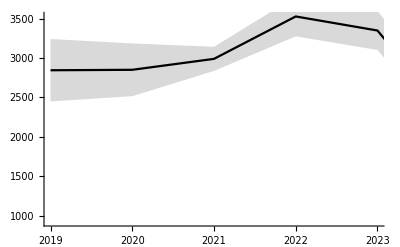

```mathematica
ErrorListPlot[
{
Transpose[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,consumptionMonthly,"Year"]]]
},
{Black},
{PlotRange->{{2019,2023},All}},
{True,True,False}
]
```

### trends

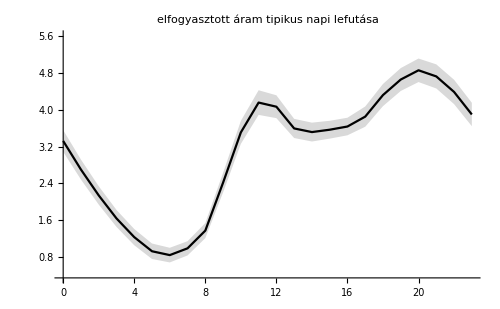

```mathematica
ErrorListPlot[
{
Transpose[Map[{#[[1]],#[[2]],#[[3]]}&,SortBy[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,consumptionHourly,"Hour"]],First]]]
},
{Black},
{PlotLabel->"elfogyasztott áram tipikus napi lefutása",ImageSize->500},
{True,True,False}
]
```

```mathematica
typicalDailyConsumptionByMonth=Table[
Transpose[
Map[
{#[[1]],#[[2]],#[[3]]}&,
SortBy[
Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,Select[
consumptionHourly,
DateValue[#[[1]],"Month"]==month&
],"Hour"]]
,First]
]
]
,{month,{10,11,12,1,2,3,4}}];
```

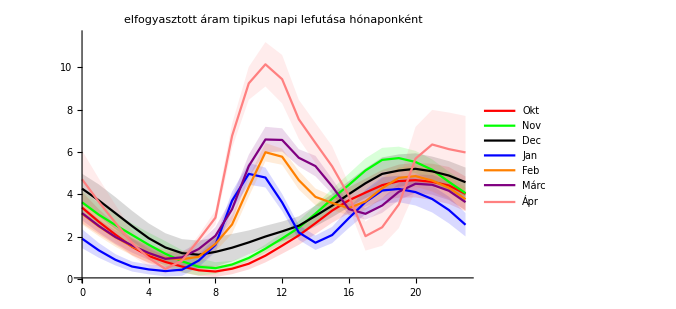

```mathematica
ErrorListPlot[
typicalDailyConsumptionByMonth,
{Red,Green,Black,Blue,Orange,Purple,Pink},
{PlotLegends->RotateLeft[monthNames,9][[1;;7]],PlotLabel->"elfogyasztott áram tipikus napi lefutása hónaponként",ImageSize->500},
{True,True,False}
]
```

```mathematica
typicalDailyConsumptionByPVPresence=Table[
Transpose[
Map[
{#[[1]],#[[2]],#[[3]]}&,
SortBy[
Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,Select[
consumptionHourly,
MemberQ[months,DateValue[#[[1]],"Month"]]&
],"Hour"]]
,First]
]
]
,{months,{{10,11,12},{1,2,3,4}}}];
```

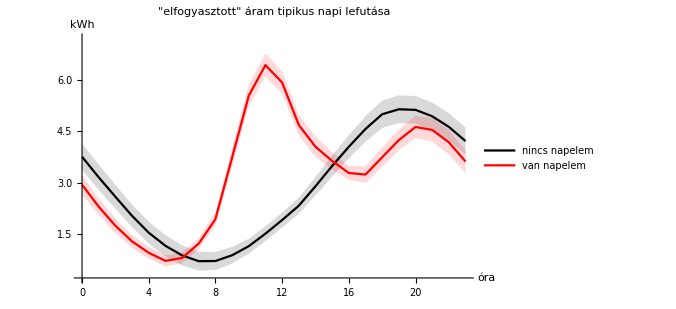

```mathematica
typicalDailyConsumptionByPVPresencePlot=ErrorListPlot[
typicalDailyConsumptionByPVPresence,
{Black,Red},
{PlotLegends->{"nincs napelem","van napelem"},PlotLabel->"\"elfogyasztott\" áram tipikus napi lefutása",ImageSize->500,AxesLabel->{"óra","kWh"}},
{True,True,False}
]
```

```mathematica
Export[NotebookDirectory[]<>"\\output\\img\\fogyasztas_napi_szetvalasztva.png",typicalDailyConsumptionByPVPresencePlot]
```

C:\Users\Beno\Documents\SZAKI\dev\aram\\output\img\fogyasztas_napi_szetvalasztva.png

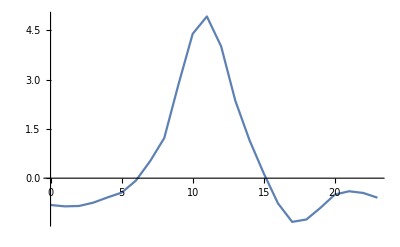

```mathematica
ListPlot[
Transpose[{
typicalDailyConsumptionByPVPresence[[1]][[1]],
typicalDailyConsumptionByPVPresence[[2]][[2]]-typicalDailyConsumptionByPVPresence[[1]][[2]]
}],Joined->True
]
```

```mathematica
Total[typicalDailyConsumptionByPVPresence[[2]][[2]]-typicalDailyConsumptionByPVPresence[[1]][[2]]]
```

11.0267

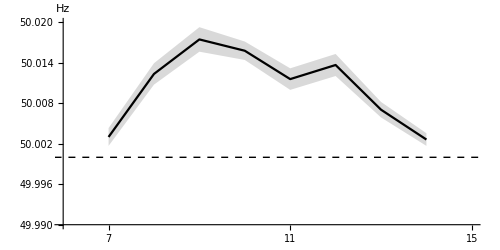

```mathematica
plotToExport=ErrorListPlot[
{
Transpose[Drop[Drop[Map[{#[[1]],#[[2]],#[[3]]}&,SortBy[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,gridFreqHourly,"Hour"]],First]],3],-4]]
},
{Black},
{ImageSize->500,PlotRange->{{7,16},{49.99,50.02}},AxesOrigin->{7,49.99},Epilog->{Dashed,Line[{{0,50},{25,50}}]},AspectRatio->0.5,Ticks->{Map[{#,#-1}&,Range[0,24,1]],Automatic},AxesLabel->{"","Hz"}},
{True,True,False}
]
```

```mathematica
Export[NotebookDirectory[]<>"output\\img\\loss\\freq.png",plotToExport]
```

C:\Users\Beno\Documents\SZAKI\dev\aram\output\img\loss\freq.png

```mathematica
typicalEntsoeLoadByMonth=Table[
Transpose[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,
Select[
entsoeLoadHourly2023,
DateValue[#[[1]],"Month"]==month&
],"Hour"]]]
,{month,Range[12]}];
```

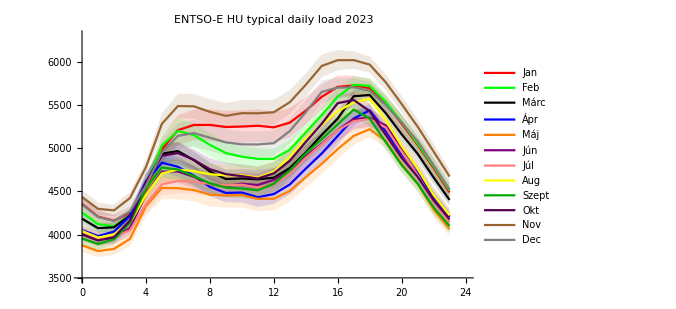

```mathematica
ErrorListPlot[
typicalEntsoeLoadByMonth,
{Red,Green,Black,Blue,Orange,Purple,Pink,Yellow,Darker[Green],Darker[Purple],Brown,Gray},
{PlotLabel->"ENTSO-E HU typical daily load 2023",ImageSize->500,Epilog->{Dashed,Line[{{0,50},{25,50}}]},PlotLegends->monthNames,PlotRange->{{0,24},{3500,6300}},AxesOrigin->{0,3500}},
{True,True,False}
]
```

```mathematica
typicalDailyTakeupByMonth=Table[
Transpose[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,
Select[
takeup15Minutes,
DateValue[#[[1]],"Month"]==month&
],"Hour"]]]
,{month,{10,11,12,1,2,3,4}}];
```

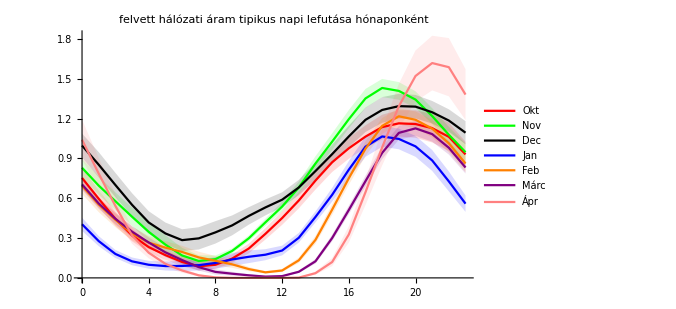

```mathematica
ErrorListPlot[
typicalDailyTakeupByMonth,
{Red,Green,Black,Blue,Orange,Purple,Pink},
{PlotLegends->RotateLeft[monthNames,9][[1;;7]],PlotLabel->"felvett hálózati áram tipikus napi lefutása hónaponként",ImageSize->500},
{True,True,False}
]
```

```mathematica
typicalDailyTakeupByPVPresence=Table[
Transpose[
Map[
{#[[1]],#[[2]],#[[3]]}&,
SortBy[
Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,Select[
takeupHourly,
MemberQ[months,DateValue[#[[1]],"Month"]]&
],"Hour"]]
,First]
]
]
,{months,{{10,11,12},{1,2,3,4}}}];
```

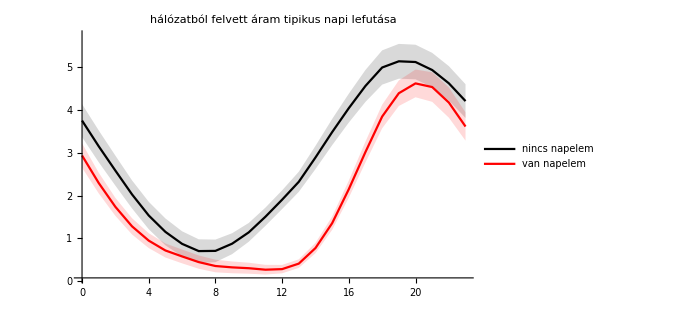

```mathematica
ErrorListPlot[
typicalDailyTakeupByPVPresence,
{Black,Red},
{PlotLegends->{"nincs napelem","van napelem"},PlotLabel->"hálózatból felvett áram tipikus napi lefutása",ImageSize->500},
{True,True,False}
]
```

```mathematica
Total[typicalDailyTakeupByPVPresence[[2]][[2]]-typicalDailyTakeupByPVPresence[[1]][[2]]]//N
```

-22.8908

```mathematica
typicalDailyProduction=Transpose[Join[{{0,0,0},{1,0,0},{2,0,0},{3,0,0}},Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,productionHourly,"Hour"]],{{20,0,0},{21,0,0},{22,0,0},{23,0,0}}]];
```

```mathematica
typicalDailyFeedin=Transpose[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,
Select[
feedin15Minutes,
MemberQ[{1,2,3,4},DateValue[#[[1]],"Month"]]&
],"Hour"]]];
```

```mathematica
expectedDailyFeedinMinusTakeup=Transpose[{Range[0,23],typicalDailyProduction[[2]]-typicalDailyConsumptionByPVPresence[[1]][[2]]}];
```

```mathematica
actualDailyFeedinMinusTakeup=Transpose[{Range[0,23],typicalDailyFeedin[[2]]-typicalDailyTakeupByPVPresence[[2]][[2]]}];
```

```mathematica
estimatedDailyLoss=typicalDailyConsumptionByPVPresence[[2]][[2]]-typicalDailyConsumptionByPVPresence[[1]][[2]];
```

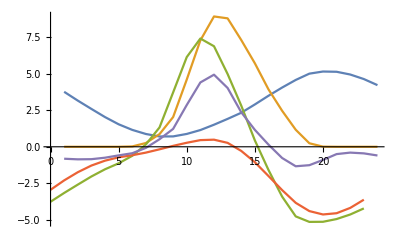

```mathematica
ListPlot[{
typicalDailyConsumptionByPVPresence[[1]][[2]],
typicalDailyProduction[[2]],
expectedDailyFeedinMinusTakeup,
actualDailyFeedinMinusTakeup,
estimatedDailyLoss
},Joined->True]
```

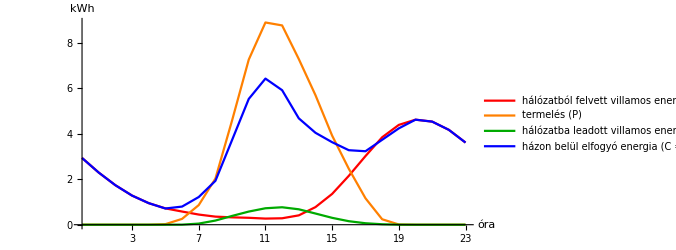

```mathematica
plotToExport=ListPlot[
{
typicalDailyTakeupByPVPresence[[2]][[2]],
typicalDailyProduction[[2]],
typicalDailyFeedin[[2]],
typicalDailyConsumptionByPVPresence[[2]][[2]]
},
PlotStyle->Map[{Thick,#}&,{Red,Orange,Darker[Green],Blue}],ImageSize->500,PlotLegends->Placed[{"hálózatból felvett villamos energia (T)","termelés (P)","hálózatba leadott villamos energia (F)","házon belül elfogyó energia (C = T + P - F)"},Bottom],
AxesLabel->{"óra","kWh"},Joined->True,PlotRange->{{1,24},All},Ticks->{Map[{#,#-1}&,Range[0,24,1]],Automatic},AspectRatio->0.5
]
```

```mathematica
Export[NotebookDirectory[]<>"output\\img\\loss\\measured_daily_typical.png",plotToExport]
```

C:\Users\Beno\Documents\SZAKI\dev\aram\output\img\loss\measured_daily_typical.png

```mathematica
Export[NotebookDirectory[]<>"output\\img\\loss\\measured_daily_typical_with_consumption.png",plotToExport]
```

C:\Users\Beno\Documents\SZAKI\dev\aram\output\img\loss\measured_daily_typical_with_consumption.png

```mathematica
N[Mean[typicalDailyConsumptionByPVPresence[[2]][[2]][[1;;4]]/typicalDailyConsumptionByPVPresence[[1]][[2]][[1;;4]]]]
```

0.703767

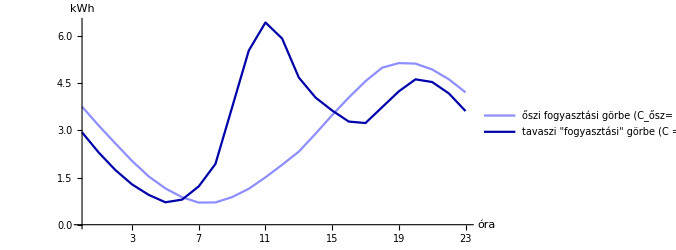

```mathematica
plotToExport=ListPlot[
{
typicalDailyConsumptionByPVPresence[[1]][[2]],
typicalDailyConsumptionByPVPresence[[2]][[2]]
},
PlotStyle->Map[{Thick,#}&,{Lighter[Lighter[Blue]],Darker[Blue]}],ImageSize->500,PlotLegends->Placed[{"őszi fogyasztási görbe (C_ősz= T_ősz)","tavaszi \"fogyasztási\" görbe (C = T + P - F)"},Bottom],
AxesLabel->{"óra","kWh"},Joined->True,PlotRange->{{1,24},All},Ticks->{Map[{#,#-1}&,Range[0,24,1]],Automatic},AspectRatio->0.5
]
```

```mathematica
Export[NotebookDirectory[]<>"output\\img\\loss\\consumption_curves.png",plotToExport]
```

C:\Users\Beno\Documents\SZAKI\dev\aram\output\img\loss\consumption_curves.png

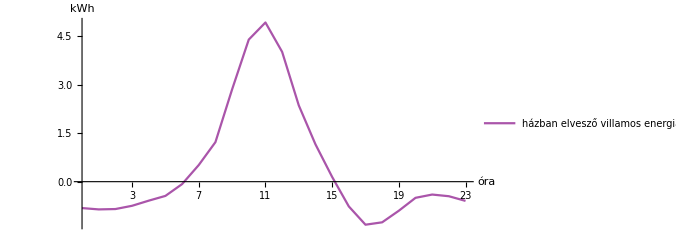

```mathematica
plotToExport=ListPlot[
{
estimatedDailyLoss
},
PlotStyle->Map[{Thick,#}&,{Lighter[Purple]}],ImageSize->500,PlotLegends->Placed[{"házban elvesző villamos energia (L = C_ősz - C)"},Bottom],
AxesLabel->{"óra","kWh"},Joined->True,PlotRange->{{1,24},All},Ticks->{Map[{#,#-1}&,Range[0,24,1]],Automatic},AspectRatio->0.5
]
```

```mathematica
Export[NotebookDirectory[]<>"output\\img\\loss\\estimated_loss.png",plotToExport]
```

C:\Users\Beno\Documents\SZAKI\dev\aram\output\img\loss\estimated_loss.png

```mathematica
Mean[Transpose[Select[Select[Transpose[{typicalDailyProduction[[1]],100Quiet[estimatedDailyLoss/typicalDailyProduction[[2]]]}],Between[#[[1]],{6,16}]&],#[[2]]>0&]][[2]]]
```

44.4251

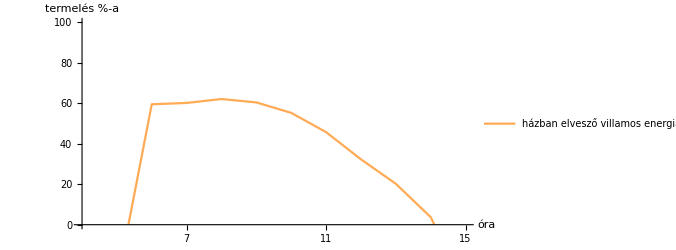

```mathematica
plotToExport=ListPlot[
{
Select[Transpose[{typicalDailyProduction[[1]],100Quiet[estimatedDailyLoss/typicalDailyProduction[[2]]]}],Between[#[[1]],{6,16}]&]
},
PlotStyle->Map[{Thick,#}&,{Lighter[Orange]}],ImageSize->500,PlotLegends->Placed[{"házban elvesző villamos energia a termelés százalékában (L / P)"},Bottom],
AxesLabel->{"óra","termelés %-a"},Joined->True,PlotRange->{{5,16},{0,100}},Ticks->{Map[{#,#-1}&,Range[0,24,1]],Automatic},AspectRatio->0.5
]
```

```mathematica
Export[NotebookDirectory[]<>"output\\img\\loss\\estimated_loss_percentage.png",plotToExport]
```

C:\Users\Beno\Documents\SZAKI\dev\aram\output\img\loss\estimated_loss_percentage.png

```mathematica
interpolatedCurve1=Interpolation[expectedDailyFeedinMinusTakeup,InterpolationOrder->1];
segments1=Quiet[{
{
0,
x/.Solve[Interpolation[expectedDailyFeedinMinusTakeup[[1;;12]],InterpolationOrder->1][x]==0,x][[1]]
},
{
x/.Solve[Interpolation[expectedDailyFeedinMinusTakeup[[1;;12]],InterpolationOrder->1][x]==0,x][[1]],x/.Solve[Interpolation[expectedDailyFeedinMinusTakeup[[12;;23]],InterpolationOrder->1][x]==0,x][[1]]
},
{
x/.Solve[Interpolation[expectedDailyFeedinMinusTakeup[[12;;23]],InterpolationOrder->1][x]==0,x][[1]],
24
}
}];
```

```mathematica
interpolatedCurve2=Interpolation[actualDailyFeedinMinusTakeup,InterpolationOrder->1];
segments2=Quiet[{
{
0,
x/.Solve[Interpolation[actualDailyFeedinMinusTakeup[[7;;11]],InterpolationOrder->1][x]==0,x][[1]]
},
{
x/.Solve[Interpolation[actualDailyFeedinMinusTakeup[[7;;11]],InterpolationOrder->1][x]==0,x][[1]],x/.Solve[Interpolation[actualDailyFeedinMinusTakeup[[13;;15]],InterpolationOrder->1][x]==0,x][[1]]
},
{
x/.Solve[Interpolation[actualDailyFeedinMinusTakeup[[13;;15]],InterpolationOrder->1][x]==0,x][[1]],
24
}
}];
```

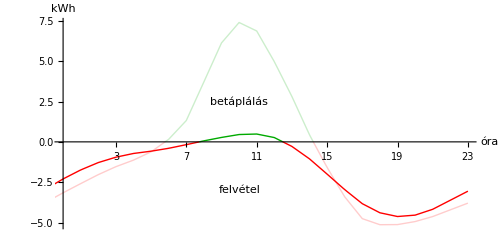

```mathematica
plotToExport=Show[{
Table[Plot[
interpolatedCurve1[h],{h,segments1[[n]][[1]],segments1[[n]][[2]]},
PlotStyle->Map[{Thick,Opacity[0.2,#]}&,{{Red,Darker[Green],Red}[[n]]}],ImageSize->500,
AxesLabel->{"óra","kWh"},PlotRange->{{1,24},All},Ticks->{Map[{#,#-1}&,Range[0,24,1]],Automatic},AspectRatio->0.5,
Epilog->{Black,FontSize->13,Text["betáplálás",{Mean[segments[[2]]],2.5}],Text["felvétel",{Mean[segments[[2]]],-3}]}
],{n,1,3}],
Table[Plot[
interpolatedCurve2[h],{h,segments2[[n]][[1]],segments2[[n]][[2]]},
PlotStyle->Map[{Thick,#}&,{{Red,Darker[Green],Red}[[n]]}],ImageSize->500,
AxesLabel->{"óra","kWh"},PlotRange->{{1,24},All},Ticks->{Map[{#,#-1}&,Range[0,24,1]],Automatic},AspectRatio->0.5,
Epilog->{Black,FontSize->13,Text["betáplálás",{Mean[segments[[2]]],2.5}],Text["felvétel",{Mean[segments[[2]]],-3}]}
],{n,1,3}]
}]
```

```mathematica
Export[NotebookDirectory[]<>"output\\img\\loss\\actual_grid_dynamics.png",plotToExport]
```

C:\Users\Beno\Documents\SZAKI\dev\aram\output\img\loss\actual_grid_dynamics.png

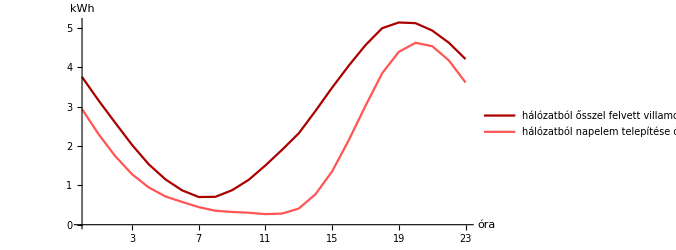

```mathematica
plotToExport=ListPlot[
{
typicalDailyTakeupByPVPresence[[1]][[2]],
typicalDailyTakeupByPVPresence[[2]][[2]]
},
PlotStyle->Map[{Thick,#}&,{Darker[Red],Lighter[Red]}],ImageSize->500,PlotLegends->Placed[{"hálózatból ősszel felvett villamos energia (T_ősz)","hálózatból napelem telepítése óta felvett villamos energia (T)"},Bottom],
AxesLabel->{"óra","kWh"},Joined->True,PlotRange->{{1,24},All},Ticks->{Map[{#,#-1}&,Range[0,24,1]],Automatic},AspectRatio->0.5
]
```

```mathematica
Export[NotebookDirectory[]<>"output\\img\\loss\\takeup_autumn_vs_pv.png",plotToExport]
```

C:\Users\Beno\Documents\SZAKI\dev\aram\output\img\loss\takeup_autumn_vs_pv.png

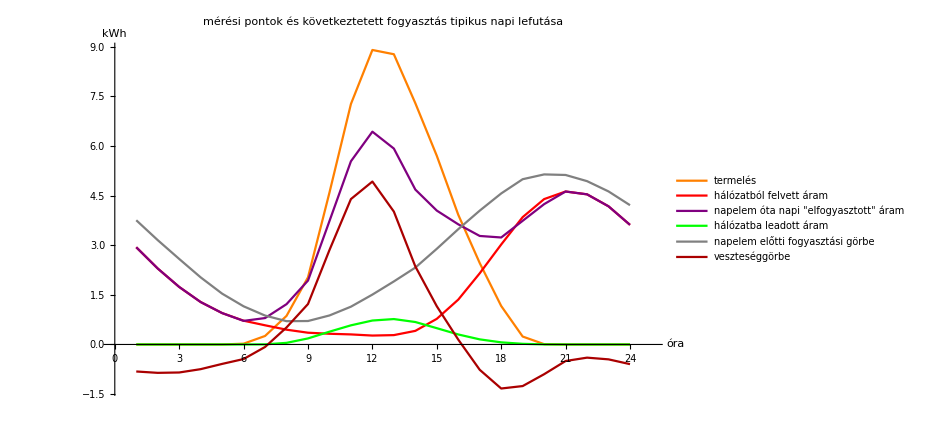

```mathematica
ListPlot[
{
typicalDailyProduction[[2]],
typicalDailyTakeupByPVPresence[[2]][[2]],
typicalDailyConsumptionByPVPresence[[2]][[2]],
typicalDailyFeedin[[2]],
typicalDailyConsumptionByPVPresence[[1]][[2]],
estimatedDailyLoss
},
PlotStyle->{Orange,Red,Purple,Green,Gray,Darker[Red]},
PlotLabel->"mérési pontok és következtetett fogyasztás tipikus napi lefutása",ImageSize->700,PlotLegends->{"termelés","hálózatból felvett áram","napelem óta napi \"elfogyasztott\" áram","hálózatba leadott áram","napelem előtti fogyasztási görbe","veszteséggörbe"},
AxesLabel->{"óra","kWh"},Joined->True,PlotRange->{{0,25},All}
]
```

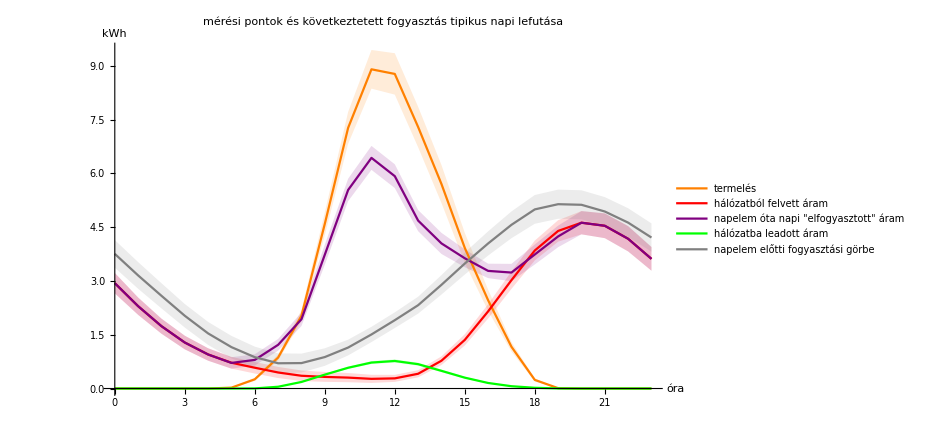

```mathematica
ErrorListPlot[
{
typicalDailyProduction,
typicalDailyTakeupByPVPresence[[2]],
typicalDailyConsumptionByPVPresence[[2]],
typicalDailyFeedin,
typicalDailyConsumptionByPVPresence[[1]]
},
{Orange,Red,Purple,Green,Gray},
{
PlotLabel->"mérési pontok és következtetett fogyasztás tipikus napi lefutása",ImageSize->700,PlotLegends->{"termelés","hálózatból felvett áram","napelem óta napi \"elfogyasztott\" áram","hálózatba leadott áram","napelem előtti fogyasztási görbe"},
AxesLabel->{"óra","kWh"}
},
{True,True,False}
]
```

```mathematica
feedinRatioHourly=MergeDateValueLists[Ratio,"Hour",{feedinHourly,productionHourly}];
```

```mathematica
typicalDailyFeedinRatio=Transpose[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,feedinRatioHourly,"Hour"]]];
```

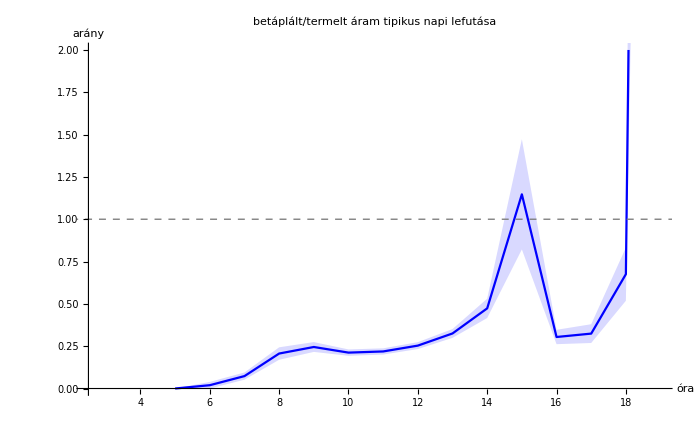

```mathematica
ErrorListPlot[
{
typicalDailyFeedinRatio
},
{Blue},
{
PlotLabel->"betáplált/termelt áram tipikus napi lefutása",ImageSize->700,PlotRange->{Automatic,{0,2}},
AxesLabel->{"óra","arány"},Epilog->{Gray,Dashed,Line[{{0,1},{24,1}}]}
},
{True,True,False}
]
```

```mathematica
feedinRatioDaily=MergeDateValueLists[Ratio,"Day",{feedinDaily,productionDaily}];
```

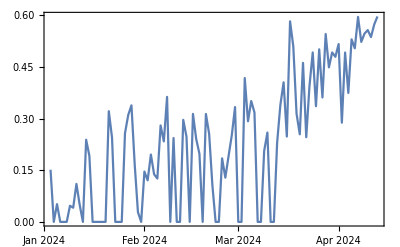

```mathematica
DateListPlot[feedinRatioDaily]
```

```mathematica
typicalWeeklyConsumptionByPVPresence=Table[
Transpose[
Map[
{#[[1]],#[[2]],#[[3]]}&,
SortBy[
Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,Select[
consumptionDaily,
MemberQ[months,DateValue[#[[1]],"Month"]]&
],"DayName"]/.{Monday->1,Tuesday->2,Wednesday->3,Thursday->4,Friday->5,Saturday->6,Sunday->7}]
,First]
]
]
,{months,{{10,11,12},{1,2,3,4}}}];
```

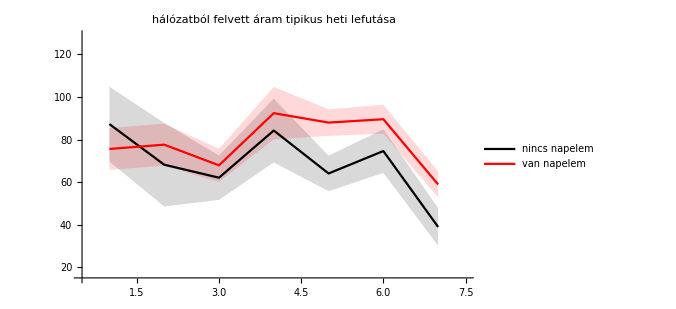

```mathematica
ErrorListPlot[
typicalWeeklyConsumptionByPVPresence,
{Black,Red},
{PlotLegends->{"nincs napelem","van napelem"},PlotLabel->"hálózatból felvett áram tipikus heti lefutása",ImageSize->500},
{True,True,False}
]
```

```mathematica
typicalDailyFeedinByMonth=Table[
Transpose[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,
Select[
feedin15Minutes,
DateValue[#[[1]],"Month"]==month&
],"Hour"]]]
,{month,{10,11,12,1,2,3,4}}];
```

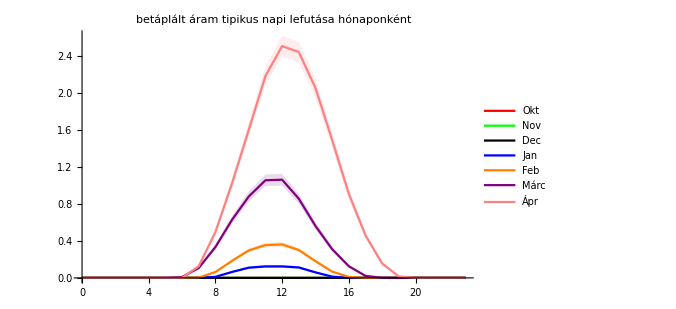

```mathematica
ErrorListPlot[
typicalDailyFeedinByMonth,
{Red,Green,Black,Blue,Orange,Purple,Pink},
{PlotLegends->RotateLeft[monthNames,9][[1;;7]],PlotLabel->"betáplált áram tipikus napi lefutása hónaponként",ImageSize->500},
{True,True,False}
]
```

```mathematica
typicalWeeklyFeedin=Transpose[SortBy[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,Select[
feedinDaily,
MemberQ[{1,2,3,4},DateValue[#[[1]],"Month"]]&
],"DayName"]]/.{Monday->1,Tuesday->2,Wednesday->3,Thursday->4,Friday->5,Saturday->6,Sunday->7},First]];
```

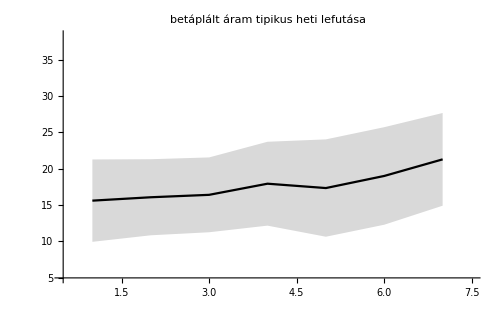

```mathematica
ErrorListPlot[
{
typicalWeeklyFeedin
},
{Black},
{PlotLabel->"betáplált áram tipikus heti lefutása",ImageSize->500},
{True,True,False}
]
```

```mathematica
typicalWeeklyTakeupByPVPresence=Table[
Transpose[SortBy[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,Select[
takeupDaily,
MemberQ[months,DateValue[#[[1]],"Month"]]&
],"DayName"]]/.{Monday->1,Tuesday->2,Wednesday->3,Thursday->4,Friday->5,Saturday->6,Sunday->7},First]]
,{months,{{10,11,12},{1,2,3,4}}}];
```

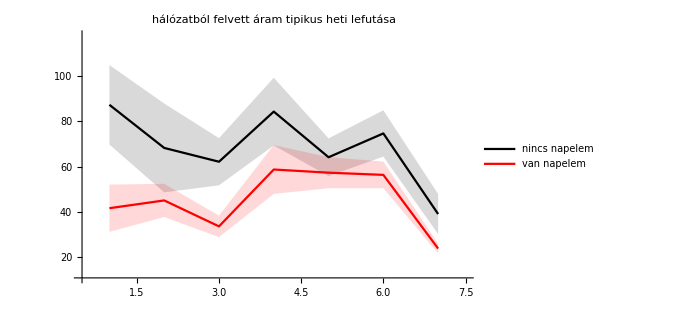

```mathematica
ErrorListPlot[
typicalWeeklyTakeupByPVPresence,
{Black,Red},
{PlotLabel->"hálózatból felvett áram tipikus heti lefutása",PlotLegends->{"nincs napelem","van napelem"},ImageSize->500},
{True,True,False}
]
```

```mathematica
typicalWeeklyProduction=Transpose[SortBy[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,productionDaily,"DayName"]]/.{Monday->1,Tuesday->2,Wednesday->3,Thursday->4,Friday->5,Saturday->6,Sunday->7},First]];
```

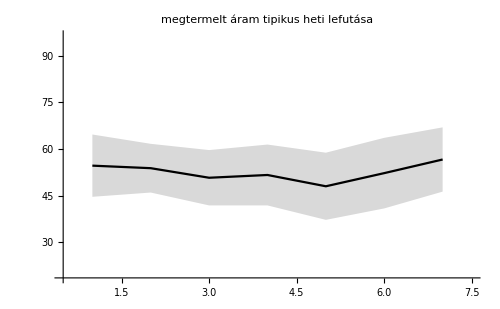

```mathematica
ErrorListPlot[
{
typicalWeeklyProduction
},
{Black},
{PlotLabel->"megtermelt áram tipikus heti lefutása",ImageSize->500},
{True,True,False}
]
```

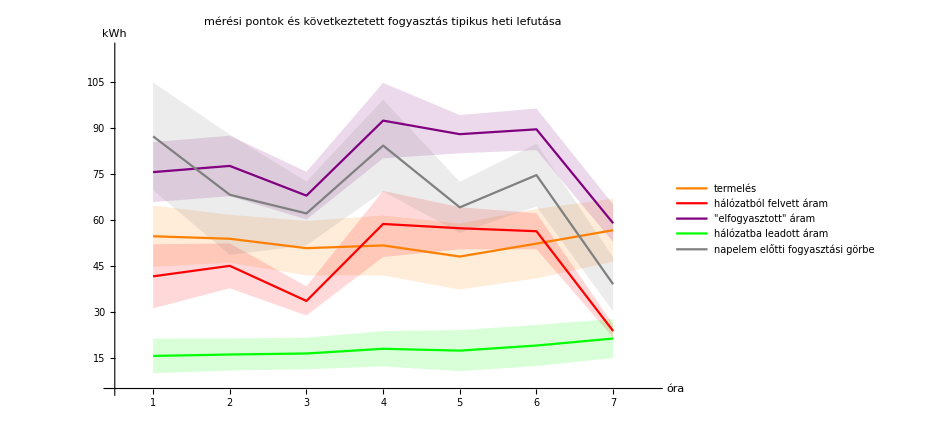

```mathematica
ErrorListPlot[
{
typicalWeeklyProduction,
typicalWeeklyTakeupByPVPresence[[2]],
typicalWeeklyConsumptionByPVPresence[[2]],
typicalWeeklyFeedin,
typicalWeeklyTakeupByPVPresence[[1]]
},
{Orange,Red,Purple,Green,Gray},
{
PlotLabel->"mérési pontok és következtetett fogyasztás tipikus heti lefutása",ImageSize->700,PlotLegends->{"termelés","hálózatból felvett áram","\"elfogyasztott\" áram","hálózatba leadott áram","napelem előtti fogyasztási görbe"},
AxesLabel->{"óra","kWh"}
},
{True,True,False}
]
```

```mathematica
typicalDailyProductionByMonth=Table[
Transpose[
Drop[
Map[
{#[[1]]+0.5,#[[2]],If[Length[#]==3,#[[3]],0]}&,
SortBy[
Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,Select[
productionHourly,
DateValue[#[[1]],"Month"]==month&
],"Hour"]]
,First]
]
,1]
]
,{month,{1,2,3,4}}];
```

```mathematica
ErrorListPlot[
typicalDailyProductionByMonth,
{Blue,Orange,Purple,Pink},
{PlotLegends->monthNames[[1;;4]],PlotLabel->"megtermelt áram tipikus napi lefutása hónaponként",ImageSize->500},
{True,True,False}
]
```

-Graphics-

```mathematica
typicalYearlyConsumption=Transpose[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,consumptionMonthly,"Month"]]]//{#[[1]],#[[2]]/1000,#[[3]]/1000}&;
```

```mathematica
Mean[typicalYearlyConsumption[[2]][[1;;4]]]/Mean[typicalYearlyConsumption[[2]][[10;;12]]]
```

0.886944

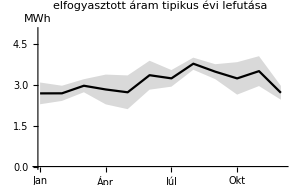

```mathematica
plotToExport=ErrorListPlot[
{
typicalYearlyConsumption
},
{Black},
{PlotLabel->"elfogyasztott áram tipikus évi lefutása",ImageSize->300,PlotRange->{{0.9,12.1},{0,5}},AxesOrigin->{0.9,0},Ticks->{Map[{#,monthNames[[#]]}&,Range[12]],Automatic},AxesLabel->{"","MWh"}},
{True,True,False}
]
```

```mathematica
Export[NotebookDirectory[]<>"output\\img\\loss\\yearly_consumption_curve.png",plotToExport]
```

C:\Users\Beno\Documents\SZAKI\dev\aram\output\img\loss\yearly_consumption_curve.png

## cash-flow, savings

```mathematica
typicalTotalYearlyConsumption=Transpose[Map[Flatten,MapFunctionToGranularity[GetMeanAndSEM,consumptionMonthly,"Month"]]][[2]];
```

```mathematica
lossFactor=0.44;
```

```mathematica
simulatedYearlyProduction=lossFactor 1000 capacityCorrection Drop[Transpose[simulatedPerformance][[-2]],2];
```

```mathematica
takeupPrice=120;
feedinPrice=80;
consumerPrice=120;
```

### monthly net metering

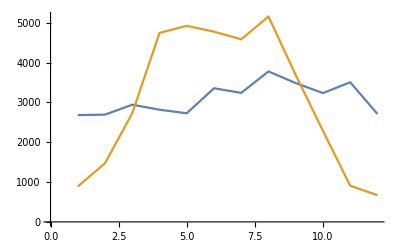

```mathematica
ListPlot[{
typicalYearlyConsumption,
simulatedYearlyProduction
},Joined->True]
```

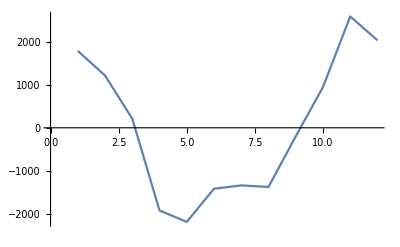

```mathematica
ListPlot[
typicalYearlyConsumption-simulatedYearlyProduction,
Joined->True
]
```

```mathematica
typicalYearlyConsumption-simulatedYearlyProduction
```

{1792.27,1218.86,213.28,-1927.7,-2194.82,-1420.95,-1344.14,-1380.22,-199.92,948.933,2596.27,2039.38}

```mathematica
Total[Table[
Module[
{monthlyConsumption,monthlyProduction,monthlyNetToGrid},
monthlyConsumption=typicalYearlyConsumption[[month]];
monthlyProduction=simulatedYearlyProduction[[month]];
monthlyNetToGrid=monthlyConsumption-monthlyProduction;
If[
monthlyNetToGrid<0,
Abs[monthlyNetToGrid]feedinPrice,
-Abs[monthlyNetToGrid]takeupPrice
]+monthlyConsumption consumerPrice
],{month,1,12}]]
```

4.0802×10^6

### yearly net metering

#### expected typical year

```mathematica
yearlyConsumption=Total[typicalTotalYearlyConsumption]//N
```

37211.

```mathematica
yearlyProduction=Total[simulatedYearlyProduction]//N
```

17055.4

```mathematica
yearlyNetToGrid=yearlyConsumption-yearlyProduction
```

20155.5

```mathematica
If[
yearlyNetToGrid<0,
Abs[yearlyNetToGrid]feedinPrice,
-Abs[yearlyNetToGrid]takeupPrice
]+yearlyConsumption consumerPrice
```

2.04665×10^6

#### expected current year

```mathematica
yearlyConsumption=Total[typicalTotalYearlyConsumption]//N
```

37211.

```mathematica
yearlyProduction=Total[Drop[simulatedYearlyProduction,-3]]//N
```

15265.7

```mathematica
yearlyNetToGrid=yearlyConsumption-yearlyProduction
```

21945.3

```mathematica
If[
yearlyNetToGrid<0,
Abs[yearlyNetToGrid]feedinPrice,
-Abs[yearlyNetToGrid]takeupPrice
]+yearlyConsumption consumerPrice
```

1.83188×10^6

#### actual current year

```mathematica
billingStart=DateObject[{2023,10,1}];
billingEnd=DateObject[{2024,10,1}];
```

```mathematica
billingPeriodConsumption=N[Total[Transpose[Select[consumptionDaily,DateBetween[#[[1]],{billingStart,billingEnd}]&]][[2]]]];
```

```mathematica
billingPeriodProduction=N[Total[Transpose[Select[productionDaily,DateBetween[#[[1]],{billingStart,billingEnd}]&]][[2]]]];
```

```mathematica
billingPeriodNetToGrid=billingPeriodConsumption-billingPeriodProduction
```

9162.

```mathematica
If[
billingPeriodNetToGrid<0,
Abs[billingPeriodNetToGrid]feedinPrice,
-Abs[billingPeriodNetToGrid]takeupPrice
]+billingPeriodConsumption consumerPrice
```

662390.

LessEqual::nordol: DateObject[{2023,10,1},Day,Gregorian,2.] and DateObject[{2023,10},Month,Gregorian,2.] cannot be compared because they are overlapping.

General::stop: Further output of LessEqual::nordol will be suppressed during this calculation.

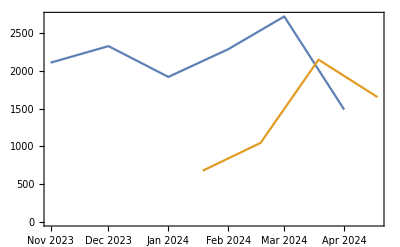

```mathematica
DateListPlot[
{
Select[consumptionMonthly,DateBetween[#[[1]],{billingStart,billingEnd}]&],
Select[productionMonthly,DateBetween[#[[1]],{billingStart,billingEnd}]&]
}
]
```